```mathematica
Integrate[Sin[x]/x,x]//N
```

SinIntegral[x]

```mathematica
Integrate[1/(√(2*Pi))*Exp[-y^2/2],{y,-2,2}]//N
```

0.9545

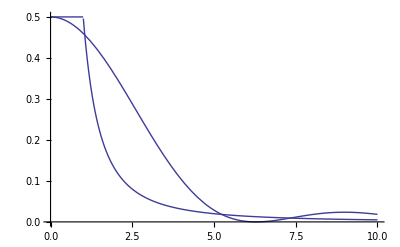

```mathematica
g[x_]:=Piecewise[{{1/2, 0≤x≤1}, {1/(2 x^2), 1<x}}]
Show[Plot[(1-Cos[x])/x^2,{x,0,10},PlotRange->All],Plot[g[x],{x,0,10},PlotRange->All]]
```